```mathematica
SetDirectory[NotebookDirectory[]];
```

# Plot options for notebook

```mathematica
SetOptions[ListContourPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
SetOptions[ListPointPlot3D,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
SetOptions[ListDensityPlot3D,{PlotTheme->"Scientific",BaseStyle->{FontSize->30}}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
colorFunc=("DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListContourPlot]));
```

# Galton watson system - Variational term 2D

Setup

### A delta function as a normalized gaussian

```mathematica
ClearAll[delta];
sigma=0.1;
delta[t_,t0_]:=Exp[-(t-t0)^2/(2*sigma^2)]/Sqrt[2.0*Pi*sigma^2];
```

### The range of nu1,nu2

```mathematica
nu1Min=-3.0;
nu1Max=0.5;
nu2Min=0.1;
nu2Max=3.0;
```

```mathematica
deltanu1=(nu1Max-nu1Min)/30.0;
deltanu2=(nu2Max-nu2Min)/30.0;
```

```mathematica
nu1Grid=Table[i,{i,nu1Min,nu1Max,deltanu1}];
nu2Grid=Table[i,{i,nu2Min,nu2Max,deltanu2}];
```

```mathematica
nu1Length=Length[nu1Grid];
nu2Length=Length[nu2Grid];
```

### The derivative functions

```mathematica
kB=0.5;
kD=1.5;
```

```mathematica
f1[nu1_,nu2_]:=nu1*(kB-kD+(kB+kD)*nu1-0.5*nu2*(kB-kD+(kB+kD)*nu1));
f2[nu1_,nu2_]:=-0.5*nu2*(kD*(-4-2*nu1+nu2)+kB*(4-2*nu1+nu2));
```

### The max time to solve until

```mathematica
tmax=2.0;
```

### IC

```mathematica
eta1=-2.5;
eta2=2.0;
```

True variational term R

### tVals to use

```mathematica
tVals=Table[tVal,{tVal,0.0,tmax,tmax/200.0}];
```

### Solve for nu, perturbing the derivative function F at the point nu by a gaussian of some magnitude

```mathematica
eps=0.1;
perturb[nu_,nuP_]:=Exp[-(nu-nuP)^2/(2*eps^2)]/Sqrt[2.0*Pi*eps^2];
```

```mathematica
nuTruePerturb[nu1P_,nu2P_,mag_,varIdx_]:=Module[{sol,n1,n2},
If[varIdx==1,
eq1=D[nu1Sol[t],t]==f1[nu1Sol[t],nu2Sol[t]]+mag*perturb[nu1Sol[t],nu1P]*perturb[nu2Sol[t],nu2P];
,
eq1=D[nu1Sol[t],t]==f1[nu1Sol[t],nu2Sol[t]];
];
If[varIdx==2,
eq2=D[nu2Sol[t],t]==f2[nu1Sol[t],nu2Sol[t]]+mag*perturb[nu1Sol[t],nu1P]*perturb[nu2Sol[t],nu2P];
,
eq2=D[nu2Sol[t],t]==f2[nu1Sol[t],nu2Sol[t]];
];

sol=NDSolve[eq1&&eq2&&Evaluate[nu1Sol[0]==eta1]&&Evaluate[nu2Sol[0]==eta2],{nu1Sol,nu2Sol},{t,0,tmax}][[1]];
n1=nu1Sol/.sol;
n2=nu2Sol/.sol;
Return[{n1,n2}]
];
```

#### Magnitude of perturbation in nu, used to evaluate the term

```mathematica
numag=0.001;
```

### Evaluate

```mathematica
r11true=Association[];
Do[
Print[nu2Vary];
Do[
r11ass=Association[];
Do[
r11ass[nuVaryMag]=nuTruePerturb[nu1Vary,nu2Vary,nuVaryMag,1][[1]];
,{nuVaryMag,-numag,numag,numag}];
Do[
r11tbl=Table[{nuVaryMag,r11ass[nuVaryMag][tVal]},{nuVaryMag,-numag,numag,numag}];
r11Interp=Interpolation[r11tbl,InterpolationOrder->2];

If[!KeyExistsQ[r11true,tVal],r11true[tVal]={}];
AppendTo[r11true[tVal],{nu1Vary,nu2Vary,Derivative[1][r11Interp][0.0]}];
,{tVal,tVals}];

,{nu1Vary,nu1Min,nu1Max,(nu1Max-nu1Min)/30.0}];
,{nu2Vary,nu2Min,nu2Max,(nu2Max-nu2Min)/30.0}];
```

0.1

0.196667

0.293333

0.39

0.486667

0.583333

0.68

0.776667

0.873333

0.97

1.06667

1.16333

1.26

1.35667

1.45333

1.55

1.64667

1.74333

1.84

1.93667

2.03333

2.13

2.22667

2.32333

2.42

2.51667

2.61333

2.71

2.80667

2.90333

3.

### Solution

```mathematica
Manipulate[
ListContourPlot[r11true[tVal],PlotRange->{-0.1,1.5},ColorFunction->ColorData[{colorFunc,{-0.1,1.5}}],ColorFunctionScaling->False],{tVal,tVals,ControlType->Manipulator}]
```

### Evaluate 2

```mathematica
r21true=Association[];
Do[
Print[nu2Vary];
Do[
r21ass=Association[];
Do[
r21ass[nuVaryMag]=nuTruePerturb[nu1Vary,nu2Vary,nuVaryMag,1][[2]];
,{nuVaryMag,-numag,numag,numag}];
Do[
r21tbl=Table[{nuVaryMag,r21ass[nuVaryMag][tVal]},{nuVaryMag,-numag,numag,numag}];
r21Interp=Interpolation[r21tbl,InterpolationOrder->2];

If[!KeyExistsQ[r21true,tVal],r21true[tVal]={}];
AppendTo[r21true[tVal],{nu1Vary,nu2Vary,Derivative[1][r21Interp][0.0]}];
,{tVal,tVals}];

,{nu1Vary,nu1Min,nu1Max,(nu1Max-nu1Min)/30.0}];
,{nu2Vary,nu2Min,nu2Max,(nu2Max-nu2Min)/30.0}];
```

0.1

0.196667

0.293333

0.39

0.486667

0.583333

0.68

0.776667

0.873333

0.97

1.06667

1.16333

1.26

1.35667

1.45333

1.55

1.64667

1.74333

1.84

1.93667

2.03333

2.13

2.22667

2.32333

2.42

2.51667

2.61333

2.71

2.80667

2.90333

3.

### Solution

```mathematica
Manipulate[
ListContourPlot[r21true[tVal],PlotRange->{-0.1,1.5},ColorFunction->ColorData[{colorFunc,{-0.1,1.5}}],ColorFunctionScaling->False],{tVal,tVals,ControlType->Manipulator}]
```

Plot true solution

```mathematica
(* Just the solution *)
```

```mathematica
{nu1True,nu2True}=nuTruePerturb[0.0,0.0,0.0,1]
```

{InterpolatingFunction[{{0., 2.}}, <>],InterpolatingFunction[{{0., 2.}}, <>]}

```mathematica
pts=Table[{(nu2True[tVal]-nu2Min)/deltanu2,nu1Length-(nu1True[tVal]-nu1Min)/deltanu1,Position[tVals,tVal][[1,1]]},{tVal,tVals}];
pltnu=ListPointPlot3D[pts]/.Point[a___]:>{Thickness[0.015],Black,Line[a]}
```

-Graphics3D-

```mathematica
pts2=Table[{tVal,nu1True[tVal],nu2True[tVal]},{tVal,tVals}];
pltnu2=ListPointPlot3D[pts2]/.Point[a___]:>{Thickness[0.01],Black,Dashed,Line[a]}
```

-Graphics3D-

Contour plot

```mathematica
(* 3d table for r21 *)
```

```mathematica
tbl3dr21=Association[];
ctr=0;
Do[
Do[
tbl3dr21[ctr]=Join[{tVal},r21true[tVal][[i]]];
ctr+=1;
,{i,1,Length[r21true[tVal]]}];
,{tVal,tVals}];
tbl3dr21=Values[tbl3dr21];
```

```mathematica
rng={0,1.0};
```

```mathematica
pltr21=ListDensityPlot3D[tbl3dr21,PlotRange->All,AspectRatio->{10,1,1},ColorFunction->ColorData[{colorFunc,rng}],OpacityFunction->Function[f,0.6*Log[(Exp[1]-1)*f+1]],OpacityFunctionScaling->False,PlotRange->{Automatic,Automatic,Automatic,rng},BaseStyle->{FontSize->18},BoxRatios->{3,1,1},Boxed->False,AxesOrigin->{0,-3,0}];
```

```mathematica
(* PlotLabel->"δν_2(t)/δF_1(ν_1,ν_2)",AxesLabel->{"t","ν_1","ν_2"} *)
```

```mathematica
pltr21Tog=Show[pltr21,pltnu2,ImageSize->400,ViewPoint->{3.29,0.43,0.6},ViewVertical->{0,0,1}]
```

-Graphics3D-

```mathematica
Export["../figures_gw_2d/r21.pdf",pltr21Tog]
```

../figures_gw_2d/r21.pdf

```mathematica
leg=BarLegend[{colorFunc,rng},LabelStyle->{FontSize->18}]
```

```mathematica
Export["../figures_gw_2d/rleg.pdf",leg]
```

../figures_gw_2d/rleg.pdf

```mathematica
tbl3dr11=Association[];
ctr=0;
Do[
Do[
tbl3dr11[ctr]=Join[{tVal},r11true[tVal][[i]]];
ctr+=1;
,{i,1,Length[r11true[tVal]]}];
,{tVal,tVals}];
tbl3dr11=Values[tbl3dr11];
```

```mathematica
pltr11=ListDensityPlot3D[tbl3dr11,PlotRange->All,AspectRatio->{10,1,1},ColorFunction->ColorData[{colorFunc,rng}],OpacityFunction->Function[f,0.6*Log[(Exp[1]-1)*f+1]],OpacityFunctionScaling->False,PlotRange->{Automatic,Automatic,Automatic,rng},BaseStyle->{FontSize->18},BoxRatios->{3,1,1},Boxed->False,AxesOrigin->{0,-3,0}];
```

```mathematica
(*PlotLabel->"δν_1(t)/δF_1(ν_1,ν_2)",AxesLabel->{"t","ν_1","ν_2"}*)
```

```mathematica
pltr11Tog=Show[pltr11,pltnu2,ImageSize->400,ViewPoint->{3.29,0.43,0.6},ViewVertical->{0,0,1}]
```

-Graphics3D-

```mathematica
Export["../figures_gw_2d/r11.pdf",pltr11Tog]
```

../figures_gw_2d/r11.pdf

Plot the true basis funcs

```mathematica
imgsize=375;
SetOptions[Plot,BaseStyle->{FontSize->18},ImageSize->imgsize];
SetOptions[ListContourPlot,BaseStyle->{FontSize->18},ImageSize->imgsize];
SetOptions[ListLinePlot,BaseStyle->{FontSize->18},ImageSize->imgsize];
SetOptions[ContourPlot,BaseStyle->{FontSize->18},ImageSize->imgsize];
```

```mathematica
(*FrameLabel->{"ν_1","ν_2"},PlotLabel->"F_1(ν_1,ν_2)"*)
```

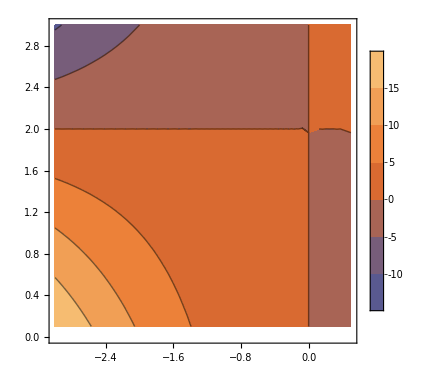

```mathematica
pltf1=ContourPlot[f1[nu1,nu2],{nu1,nu1Min,nu1Max},{nu2,nu2Min,nu2Max},PlotRange->{-12,20},ColorFunction->ColorData[{colorFunc,{-12,20}}],ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->18}]]
```

```mathematica
Export["../figures_gw_2d/f1.pdf",pltf1]
```

../figures_gw_2d/f1.pdf

```mathematica
(*FrameLabel->{"ν_1","ν_2"},PlotLabel->"F_2(ν_1,ν_2)"*)
```

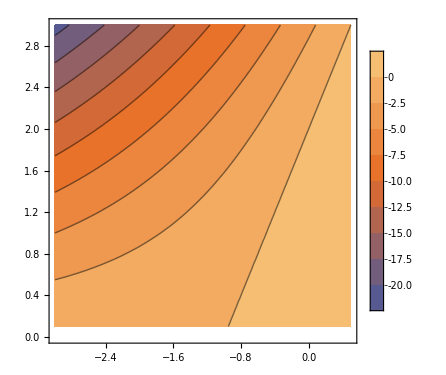

```mathematica
pltf2=ContourPlot[f2[nu1,nu2],{nu1,nu1Min,nu1Max},{nu2,nu2Min,nu2Max},PlotRange->{-22,3},ColorFunction->ColorData[{colorFunc,{-22,3}}],ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->18}]]
```

```mathematica
Export["../figures_gw_2d/f2.pdf",pltf2]
```

../figures_gw_2d/f2.pdf

Alternative (OLD): Image 3d plot

```mathematica
(* Image3d version *)
```

```mathematica
tbl3d={};
Do[
arr=ConstantArray[0.0,{nu1Length,nu2Length}];
Do[
arr[[Position[nu1Grid,r21true[tVal][[i,1]]][[1,1]],Position[nu2Grid,r21true[tVal][[i,2]]][[1,1]]]]=r21true[tVal][[i,3]];
,{i,1,Length[r21true[tVal]]}];
AppendTo[tbl3d,arr];
,{tVal,Reverse[tVals]}];
```

```mathematica
tticks={{0,"0"},{20,"0.2"},{40,"0.4"},{60,"0.6"},{80,"0.8"},{100,"1.0"}};
```

```mathematica
nu1ticks={{0,nu1Max},{10,NumberForm[nu1Max+(nu1Min-nu1Max)/3.0,{10,2}]},{20,NumberForm[nu1Max+2*(nu1Min-nu1Max)/3.0,{10,2}]},{30,nu1Min}}
```

{{0,0.5},{10,-0.67},{20,-1.83},{30,-3.}}

```mathematica
nu2ticks={{0,nu2Min},{10,NumberForm[nu2Min+(nu2Max-nu2Min)/3.0,{10,2}]},{20,NumberForm[nu2Min+2*(nu2Max-nu2Min)/3.0,{10,2}]},{30,nu2Max}}
```

{{0,0.1},{10,1.07},{20,2.03},{30,3.}}

```mathematica
nu2ticks={{0,0.1},{10,"1.0"},{20,"2.0"},{30,3.}}
```

{{0,0.1},{10,1.0},{20,2.0},{30,3.}}

```mathematica
pltr21IMG=Show[
Image3D[tbl3d,ColorFunction->"RainbowOpacity"]
,
pltnu
,
Boxed->True,Axes->True,AxesLabel->{"ν_2","ν_1","t"},BaseStyle->{FontSize->18},Ticks->{nu2ticks,nu1ticks,tticks}]
```

-Graphics3D-

### r11

```mathematica
(* 3d table for r11 *)
```

```mathematica
tbl3dr11={};
Do[
arr=ConstantArray[0.0,{nu1Length,nu2Length}];
Do[
arr[[Position[nu1Grid,r11true[tVal][[i,1]]][[1,1]],Position[nu2Grid,r11true[tVal][[i,2]]][[1,1]]]]=r11true[tVal][[i,3]];
,{i,1,Length[r11true[tVal]]}];
AppendTo[tbl3dr11,arr];
,{tVal,Reverse[tVals]}];
```

```mathematica
pltr11IMG=Show[
Image3D[tbl3dr11,ColorFunction->"RainbowOpacity"]
,
pltnu
,
Boxed->True,Axes->True,AxesLabel->{"ν_2","ν_1","t"},BaseStyle->{FontSize->18},Ticks->{nu2ticks,nu1ticks,tticks}]
```

-Graphics3D-